# Rabi Flopping, the RWA approximation, and the Hadamard Gate

In Eq. 7.34 we considered the Hamiltonian H=h_0+ H_I where 

                                 h_0= - 1/2ℏ ω_0σ_Z  and  H_I= -ℏ Δ Cos(ω t + δ)σ_X     

Below we numerically solve for the time development operator, in the interaction picture,  for different values of parameter ω_0, the frequency associated with the non-interacting qubit, Δ the Rabi coupling energy of the electric field, or frequency, and δ, the polarization parameter for the external electric field. We use dimensionless units so that ℏ=1, and set the frequency parameter ω_0=100. Parameter ξ is the ratio ω/ω_0,  η is the ratio Δ/ω_0.  At resonance, ξ=1, and is the regime (for sufficiently small values of η) in which the RWA approximation is valid.

```mathematica
ClearAll["Global`*"];
```

View source code below

```mathematica
UT[t_,ξ_,η_,δ_]:=Module[{ℏ=1,ω0=100.0,Δ,ω,sol1,sol2},
Δ=ω0 η;ω=ω0 ξ;
sol1=Flatten[NDSolve[{ⅈ ℏ psi1'[t1]==-ⅇ^(-ⅈ t1 ω0) Δ ℏ Cos[δ+t1 ω] psi2[t1],ⅈ ℏ psi2'[t1]==-ⅇ^(ⅈ t1 ω0) Δ ℏ Cos[δ+t1 ω] psi1[t1],psi1[0.0]==1.0,psi2[0.0]==0.0},{psi1,psi2},{t1,0.0,4.0Pi/ω0/η}]];
sol2=Flatten[NDSolve[{ⅈ ℏ psi1'[t1]==-ⅇ^(-ⅈ t1 ω0) Δ ℏ Cos[δ+t1 ω] psi2[t1],ⅈ ℏ psi2'[t1]==-ⅇ^(ⅈ t1 ω0) Δ ℏ Cos[δ+t1 ω] psi1[t1],psi1[0.0]==0.0,psi2[0.0]==1.0},{psi1,psi2},{t1,0.0,4.0Pi/ω0/η}]];tRabi=4.0Pi/ω0/η;Transpose[{({psi1[t],psi2[t]} /. sol1 ),({psi1[t],psi2[t]} /. sol2)}]];
RWA[t_,η_,δ_]:=Module[{ω0=100},Δ=η ω0;{{Cos[Δ/2 t],I Exp[I δ]Sin[Δ/2 t]},{I Exp[I δ]Sin[Δ/2 t],Cos[Δ/2 t]}}];
UT[1.0,1.0,0.1,0.0];
g1[i_,j_,Δ_,δ_]:=Plot[{Evaluate[Re[RWA[t,Δ,0][[i,j]]]],Evaluate[Im[RWA[t,Δ,0][[i,j]]]]},{t,0,4Pi},PlotStyle->{{Dashed,Red},{Dashed,Green}},PlotRange->{-1,1},Frame->True,FrameStyle->Directive[Orange,Dashed],FrameTicks->{False,True},ImageSize->Small];
g2[i_,j_,ξ_,Δ_,δ_]:=Plot[{Evaluate[Re[UT[t,ξ,Δ,δ][[i,j]]]],Evaluate[Im[Evaluate[UT[t,1.0,Δ,0][[i,j]]]]],Evaluate[Re[RWA[t,Δ,0][[i,j]]]],Evaluate[Im[RWA[t,Δ,0][[i,j]]]]},{t,0,tRabi},PlotStyle->{{Thick,Red},{Thick,Green},{Dashed,Red},{Dashed,Green}},PlotRange->{-1,1},Frame->True,FrameStyle->Directive[Orange,Dashed],FrameTicks->{False,True},ImageSize->Small]
```

The output consists of a table, in matrix form, for the interaction picture unitary gate U_I(t,t_0) t_0=0, so that matrix Eq. (7.40) which has the analytic form

(Cos(Δ/t) | i exp(i δ) Sin(Δ/t)
i exp(-i δ) Sin(Δ/t) | Cos(Δ/t))
looks like, for Δ=1,δ=0.

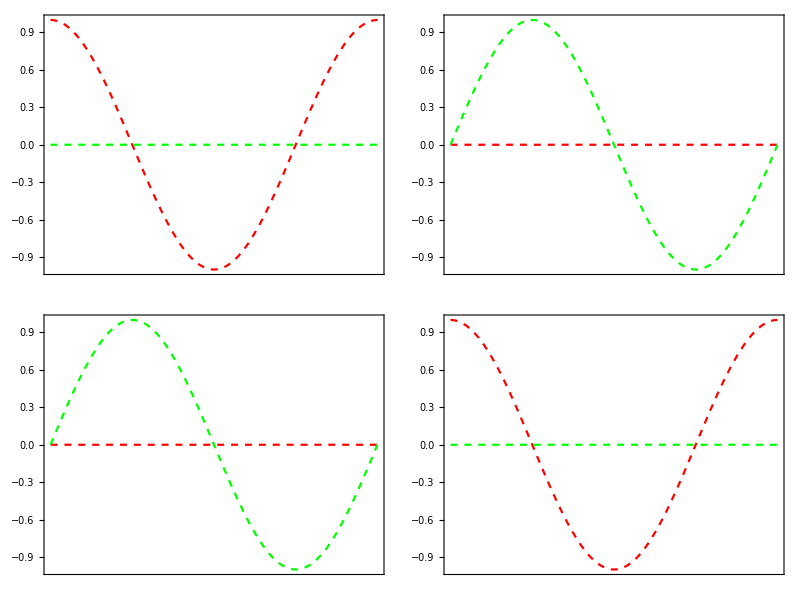
(-Graphics-)

```mathematica
MatrixForm[Table[g1[i,j,0.01,0],{i,1,2},{j,1,2}] ]
```

In this figure each quadrant represents an element of the matrix U_I(t). The red dashed lines represent the real part of the matrix, and the green dashed lines the imaginary part. The horizontal axis ranges from t=0 to t=4 π/Δ, the so called Rabi period of the oscillations. In the simulation given below, we superimpose the RWA results (dashed lines) with those obtained from an exact numerical (for a two-state system) calculation for  U_I(t) .

```mathematica
Manipulate[MatrixForm[Table[g2[i,j,ξ,β,δ],{i,1,2},{j,1,2}] ],{{ξ,1.0,"Resonance parameter"},{1.0,0.9,1.1}},{{δ,-Pi,"Polarization parameter"},{-Pi,-Pi/2,0,Pi/2,Pi}},{{β,0.1,"Rabi coupling parameter"},{0.1,0.2,0.5,0.8}},SaveDefinitions->True]
```

## Hadamard Gate

To construct the Hadamard gate, we multiply the interaction picture time development operator U_I with exp(-i h_0t), as in Eq. (7.41) of the text. We choose δ=3π/2, Δ=ω_0/6, as given in the text. We turn on the laser pulse at t=0 and shut it off at t=3π/ω_0. We numerically calculate the computational basis unitary time development operator to get (Note: we fixed ω0=100 in the code that calculates UT)

```mathematica
σZ={{1,0},{0,-1}};
Had=MatrixExp[I ω0 σZ/2 T]. UT[T,1,1/6,3π/2] /. {ω0->100,T->3π/100} ;
% // MatrixForm
```

(0.0884034-0.707591 ⅈ | 4.2181×10^-7-0.70107 ⅈ
-4.2181×10^-7-0.70107 ⅈ | 0.0884034+0.707591 ⅈ)

Let’s compare this result with the one given by Eq. (7.44), given in the text, and predicted by the RWA approximation.

```mathematica
RWAHad=-I HadamardMatrix[2]
```

{{-ⅈ/(√2),-ⅈ/(√2)},{-ⅈ/(√2),ⅈ/(√2)}}

```mathematica
Chop[Had-RWAHad] // MatrixForm
```

(0.0884034-0.000484692 ⅈ | 4.2181×10^-7+0.00603666 ⅈ
-4.2181×10^-7+0.00603666 ⅈ | 0.0884034+0.000484692 ⅈ)

Notice that the difference between the two expressions  is small  (on the order of 9 percent) but not identically zero. Why is that the case?  Can you find laser parameters for the given value ω_0that give a better approximation to the Hadamard gate?